## Homework 5

## Computational Exercise 1

1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1Original Relation

-Graphics-

1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1Symmetric Subelation

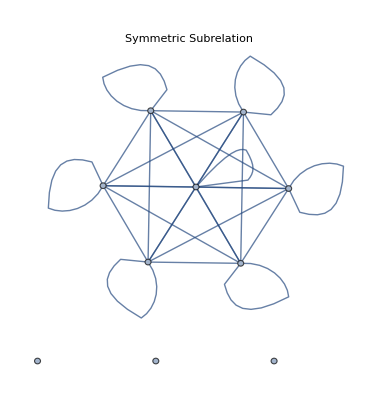

```mathematica
ClearAll[result]
subsym[x_] := Module[{result=Table[Table[0, Length[x]], Length[x]]},
Do[If[x[[i]][[j]] == 1 && x[[j]][[i]] == 1,
result[[i]][[j]] = 1,
0], {i, 1, Length[x]}, {j, 1, Length[x]}];
result
]
x = Table[{1,0,1,1,0,1,1,1,0,1}, 10];
x//Labeled[TableForm[#],"Original Relation"]&
AdjacencyGraph[x, PlotLabel->"Graph of original adjacency matrix"]
s = subsym[x];
s//Labeled[TableForm[#],"Symmetric Subelation"]&
AdjacencyGraph[s, PlotLabel->"Symmetric Subrelation"]
```

## Compuational Exercise 2

```mathematica
adjMatrix = Table[RandomChoice[{0, 1},5], 5]
adjMatrix//Labeled["Adjacency Matrix", TableForm[#]]&
adjGraph = AdjacencyGraph[adjMatrix, PlotLabel->"Adjacency Graph"]
```

{{1,1,0,1,0},{1,1,0,1,0},{0,1,1,0,1},{1,0,0,0,0},{0,0,1,1,1}}

Adjacency Matrix1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1

-Graphics-